```mathematica
Select[deps2,Chrom[#[[1]]]>Chrom[#[[2]]]&]
```

{{6,18,{2,3<->5,1<->4}},{7,18,{2,1<->5,2<->7}},{11,38,{2,3<->6,2<->4}},{11,36,{2,3<->4,6<->8}},{14,38,{2,3<->5,4<->7}},{15,38,{2,3<->5,4<->7}},{15,36,{2,5<->6,4<->8}},{18,46,{2,2<->5,6<->7}},{19,36,{2,5<->6,2<->4}},{20,38,{2,3<->6,2<->4}}}

```mathematica
HandleGraph[g_, h_, title_, size_]:={Graph[g,GraphLayout->"PlanarEmbedding", VertexLabels->"Name", GraphHighlight->h,PlotLabel->title <> ToString[ChromaticPolynomial[g,4]/24]],Grid[{PadRight[CompleteBaseCoeff[ChromaticPolynomial[g,x]],size]},ItemSize->2]}
```

```mathematica
{0,0,0,0,12,45,41,12,1}
```

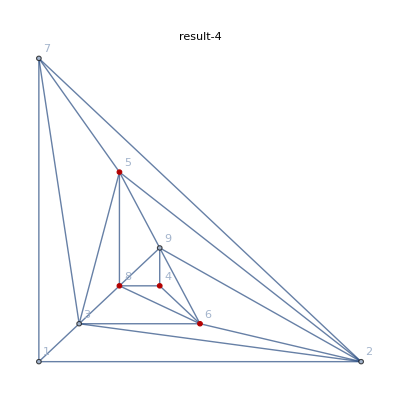
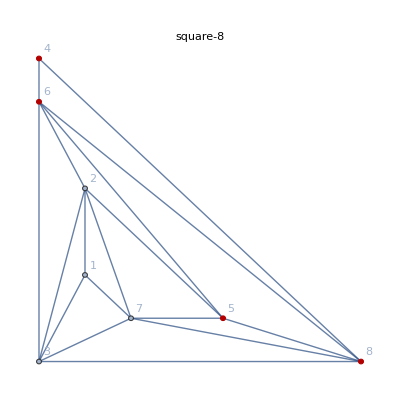
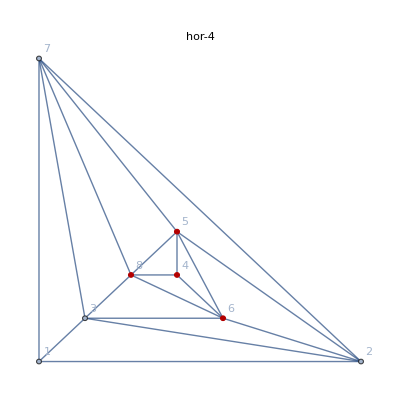
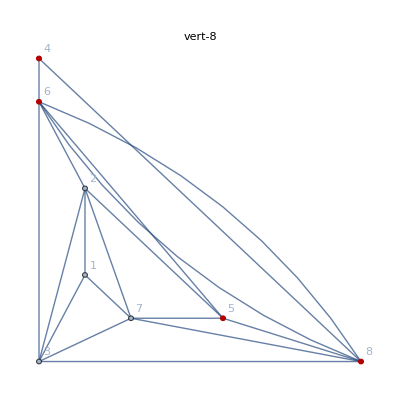
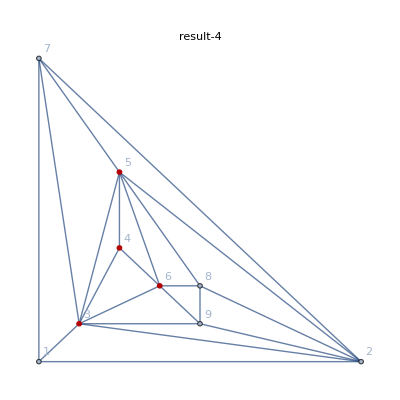
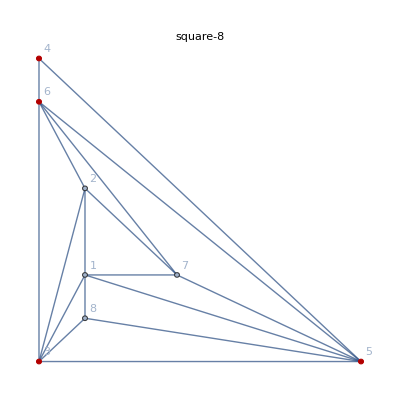
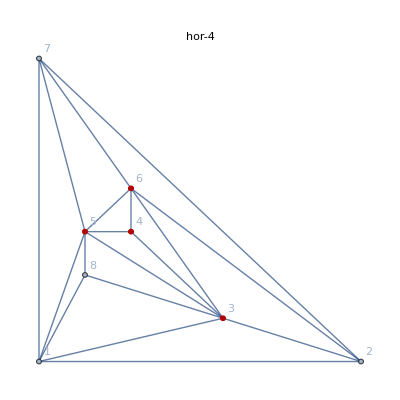
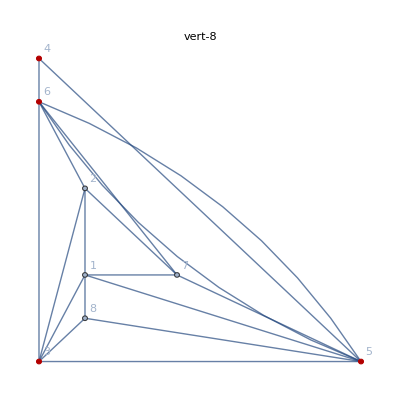
{4<->5 | 6<->8
-Graphics- | 0 | 0 | 0 | 0 | 4 | 48 | 103 | 67 | 15 | 1
-Graphics- | 0 | 0 | 0 | 0 | 8 | 31 | 33 | 11 | 1 | 0
 | 0 | 0 | 0 | 0 | 32 | 163 | 229 | 110 | 19 | 1
-Graphics- | 0 | 0 | 0 | 0 | 4 | 22 | 27 | 10 | 1 | 0
-Graphics- | 0 | 0 | 0 | 0 | 8 | 31 | 33 | 11 | 1 | 0,3<->4 | 5<->6
-Graphics- | 0 | 0 | 0 | 0 | 4 | 48 | 103 | 67 | 15 | 1
-Graphics- | 0 | 0 | 0 | 0 | 8 | 31 | 33 | 11 | 1 | 0
 | 0 | 0 | 0 | 0 | 32 | 163 | 229 | 110 | 19 | 1
-Graphics- | 0 | 0 | 0 | 0 | 4 | 22 | 27 | 10 | 1 | 0
-Graphics- | 0 | 0 | 0 | 0 | 8 | 31 | 33 | 11 | 1 | 0,3<->5 | 4<->8
-Graphics- | 0 | 0 | 0 | 0 | 9 | 68 | 120 | 70 | 15 | 1
-Graphics- | 0 | 0 | 0 | 0 | 8 | 36 | 35 | 11 | 1 | 0
 | 0 | 0 | 0 | 0 | 32 | 188 | 246 | 112 | 19 | 1
-Graphics- | 0 | 0 | 0 | 0 | 4 | 22 | 27 | 10 | 1 | 0
-Graphics- | 0 | 0 | 0 | 0 | 3 | 26 | 29 | 10 | 1 | 0,2<->6 | 3<->7
-Graphics- | 0 | 0 | 0 | 0 | 5 | 55 | 109 | 68 | 15 | 1
-Graphics- | 0 | 0 | 0 | 0 | 5 | 29 | 33 | 11 | 1 | 0
 | 0 | 0 | 0 | 0 | 20 | 150 | 227 | 110 | 19 | 1
-Graphics- | 0 | 0 | 0 | 0 | 4 | 22 | 27 | 10 | 1 | 0
-Graphics- | 0 | 0 | 0 | 0 | 1 | 15 | 25 | 10 | 1 | 0,3<->6 | 2<->4
-Graphics- | 0 | 0 | 0 | 0 | 3 | 55 | 113 | 69 | 15 | 1
-Graphics- | 0 | 0 | 0 | 0 | 6 | 32 | 34 | 11 | 1 | 0
 | 0 | 0 | 0 | 0 | 24 | 166 | 236 | 111 | 19 | 1
-Graphics- | 0 | 0 | 0 | 0 | 4 | 22 | 27 | 10 | 1 | 0
-Graphics- | 0 | 0 | 0 | 0 | 5 | 25 | 28 | 10 | 1 | 0}

```mathematica
Map[
With[{g=ReadGrof[#[[1]]], edges=Read[StringToStream[#[[3]]]]},
With[
{h={edges[[2,1]],edges[[3,1]],edges[[2,2]],edges[[3,2]]}, size=VertexCount[g]+2},
Framed[TableForm[
{{edges[[2]],edges[[3]]},
HandleGraph[ReadGrof[#[[2]]],h, "result-", size],
HandleGraph[EdgeDelete[g,edges[[2]]],h, "square-", size],
{"",Grid[{PadRight[CompleteBaseCoeff[ChromaticPolynomial[EdgeDelete[g,edges[[2]]],x]*x],size]}, ItemSize->2]},
HandleGraph[g,h, "hor-", size],

HandleGraph[EdgeAdd[EdgeDelete[g,edges[[2]]],edges[[3]]],h, "vert-", size] 
},TableAlignments->Right]]
]
]&,Take[deps2,-5]]
```

```mathematica
ChromaticPolynomial[ReadGrof[38],4]
```

72

```mathematica
ChromaticPolynomial[ReadGrof[11],4]
```

120

```mathematica
ChromaticPolynomial[EdgeDelete[ReadGrof[11],3<->6],4]
```

144

```mathematica
ChromaticPolynomial[EdgeAdd[EdgeDelete[ReadGrof[11],3<->6],2<->4],4]
```

96

```mathematica
ChromaticPolynomial[EdgeDelete[ReadGrof[6],3<->5],4]
```

144

```mathematica
ChromaticPolynomial[EdgeAdd[EdgeDelete[ReadGrof[6],3<->5],1<->4],4]
```

120

```mathematica
ChromaticPolynomial[ReadGrof[6],4]
```

96

```mathematica
ChromaticPolynomial[ReadGrof[18],4]
```

72

```mathematica
ChromaticPolynomial[EdgeAdd[EdgeDelete[ReadGrof[7],1<->5],2<->7],4]
```

96

```mathematica
ChromaticPolynomial[ReadGrof[7],4]
```

120

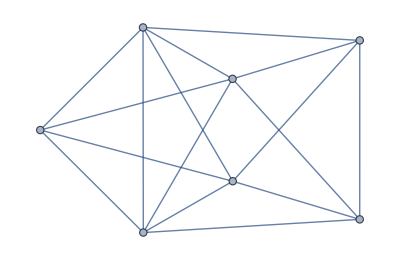

```mathematica
EdgeAdd[ReadGrof[7],2<->7]
```

```mathematica
Solve[(a==2b-c-d)&&(b≥c)&&(b≥d)&&(c≥a)&&(d≥=a) ,{a,b,c,d}]
```

```mathematica
Solve[(a==2b-c-d)&&(b≥c)&&(b≥d)&&(c≥a)&&(d≥a) && a≥0&&b≥0&&c≥0&&d≥0
 ,a]
```

{{a→ConditionalExpression[2 b-c-d,(2 b-2 d<c<b&&(3 d)/2<b<2 d&&d>0)||(1/2 (2 b-d)<c<b&&d<b<(3 d)/2&&d>0)]}}

```mathematica
With[{g=-Graphics-},
{PadRight[CompleteBaseCoeff[ChromaticPolynomial[g,x]*(x-2)],VertexCount[g]]-PadRight[CompleteBaseCoeff[ChromaticPolynomial[g,x]],VertexCount[g]]}
]
```

{{0,0,0,0,6,70,134,78}}

```mathematica
MyCheck1[square_,hor_,vert_]:=Block[
{sq= ChromaticPolynomial[square,4]/24,
h= ChromaticPolynomial[hor,4]/24,
v= ChromaticPolynomial[vert,4]/24},
Return[{2*sq>= h+v+Max[{Floor[h/2],Floor[v/2]}]}]
]
```

```mathematica
MyCheck2[square_,hor_,vert_]:=Block[
{sq= ChromaticPolynomial[square,4]/24,
h= ChromaticPolynomial[hor,4]/24,
v= ChromaticPolynomial[vert,4]/24},
Return[{2*sq> h+v+Min[{Floor[h/2],Floor[v/2]}]}]
]
```

```mathematica
HandleGraph2[g_]:=ChromaticPolynomial[g,4]/24
```

```mathematica
ChromaticPolynomial[CompleteGraph[1],x]
```

x

```mathematica
deps2=ReadList["D:\\Grofs\\dependencies2.txt",Expression];Length[deps2]
```

1365053

```mathematica
MyCheck[CompleteGraph[5],CompleteGraph[5],CompleteGraph[5]]
```

False

```mathematica
TableForm[
Sort[
DeleteDuplicates[
Monitor[
Table[
If[k%1000==0,FrontEndExecute[FrontEndToken["Save"]]];
With[{g=ReadGrof[deps2[[k,1]]], edges=Read[StringToStream[deps2[[k,3]]]]},
With[
{h={}, size=1, square = EdgeDelete[g,edges[[2]]],
ver=EdgeAdd[EdgeDelete[g,edges[[2]]],edges[[3]]]},
{
HandleGraph2[ReadGrof[deps2[[k,2]]]],
HandleGraph2[square],
HandleGraph2[g],

HandleGraph2[ver] ,
MyCheck1[square,g,ver],
MyCheck2[square,g,ver]
}
]
],
{k,Range[EndMPG[[8]]]}
],N[k/EndMPG[[8]]*100]]
]
]
]
```

1 | 2 | 1 | 2 | True | True
2 | 4 | 2 | 4 | True | True
2 | 4 | 3 | 3 | True | True
3 | 6 | 3 | 6 | True | True
3 | 6 | 4 | 5 | True | True
3 | 6 | 5 | 4 | True | True
4 | 3 | 1 | 1 | True | True
4 | 8 | 4 | 8 | True | True
4 | 8 | 5 | 7 | True | True
4 | 8 | 6 | 6 | True | True
4 | 8 | 7 | 5 | True | True
5 | 5 | 1 | 4 | True | True
5 | 5 | 2 | 3 | True | True
5 | 5 | 3 | 2 | True | True
5 | 5 | 4 | 1 | True | True
5 | 10 | 5 | 10 | True | True
5 | 10 | 6 | 9 | True | True
5 | 10 | 9 | 6 | True | True
6 | 7 | 2 | 6 | True | True
6 | 7 | 3 | 5 | True | True
6 | 7 | 5 | 3 | True | True
6 | 7 | 6 | 2 | True | True
6 | 12 | 6 | 12 | True | True
6 | 12 | 7 | 11 | True | True
6 | 12 | 9 | 9 | True | True
6 | 12 | 11 | 7 | True | True
7 | 9 | 5 | 6 | True | True
7 | 9 | 6 | 5 | True | True
7 | 14 | 7 | 14 | True | True
7 | 14 | 8 | 13 | True | True
7 | 14 | 9 | 12 | True | True
7 | 14 | 10 | 11 | True | True
7 | 14 | 11 | 10 | True | True
7 | 14 | 12 | 9 | True | True
7 | 14 | 13 | 8 | True | True
8 | 6 | 2 | 2 | True | True
8 | 11 | 5 | 9 | True | True
8 | 11 | 6 | 8 | True | True
8 | 11 | 7 | 7 | True | True
8 | 11 | 8 | 6 | True | True
8 | 11 | 9 | 5 | True | True
8 | 16 | 11 | 13 | True | True
8 | 16 | 12 | 12 | True | True
9 | 8 | 2 | 5 | True | True
9 | 8 | 3 | 4 | True | True
9 | 8 | 4 | 3 | True | True
9 | 8 | 5 | 2 | True | True
9 | 13 | 5 | 12 | True | True
9 | 13 | 12 | 5 | True | True
9 | 18 | 9 | 18 | True | True
9 | 18 | 13 | 14 | True | True
9 | 18 | 14 | 13 | True | True
10 | 10 | 2 | 8 | True | True
10 | 10 | 5 | 5 | True | True
10 | 10 | 6 | 4 | True | True
10 | 10 | 8 | 2 | True | True
10 | 15 | 6 | 14 | True | True
10 | 15 | 9 | 11 | True | True
10 | 15 | 11 | 9 | True | True
10 | 15 | 14 | 6 | True | True
10 | 20 | 14 | 16 | True | True
10 | 20 | 16 | 14 | True | True
11 | 12 | 4 | 9 | True | True
11 | 12 | 6 | 7 | True | True
11 | 12 | 7 | 6 | True | True
11 | 12 | 9 | 4 | True | True
11 | 17 | 9 | 14 | True | True
11 | 17 | 14 | 9 | True | True
11 | 22 | 11 | 22 | True | True
11 | 22 | 12 | 21 | True | True
11 | 22 | 13 | 20 | True | True
11 | 22 | 20 | 13 | True | True
11 | 22 | 21 | 12 | True | True
12 | 9 | 1 | 5 | True | True
12 | 9 | 3 | 3 | True | True
12 | 9 | 5 | 1 | True | True
12 | 14 | 9 | 7 | True | True
12 | 19 | 13 | 13 | True | True
12 | 24 | 12 | 24 | True | True
12 | 24 | 16 | 20 | True | True
12 | 24 | 20 | 16 | True | True
13 | 11 | 3 | 6 | True | True
13 | 11 | 6 | 3 | True | True
13 | 16 | 6 | 13 | True | True
13 | 16 | 7 | 12 | True | True
13 | 16 | 12 | 7 | True | True
13 | 16 | 13 | 6 | True | True
13 | 26 | 13 | 26 | True | True
14 | 13 | 3 | 9 | True | True
14 | 13 | 5 | 7 | True | True
14 | 13 | 7 | 5 | True | True
14 | 13 | 9 | 3 | True | True
14 | 18 | 6 | 16 | True | True
14 | 18 | 9 | 13 | True | True
14 | 18 | 16 | 6 | True | True
14 | 23 | 11 | 21 | True | True
14 | 23 | 21 | 11 | True | True
14 | 28 | 14 | 28 | True | True
15 | 15 | 3 | 12 | True | True
15 | 15 | 11 | 4 | True | True
15 | 15 | 12 | 3 | True | True
15 | 20 | 11 | 14 | True | True
15 | 20 | 14 | 11 | True | True
15 | 25 | 13 | 22 | True | True
15 | 30 | 20 | 25 | True | True
15 | 30 | 25 | 20 | True | True
16 | 12 | 2 | 6 | True | True
16 | 12 | 4 | 4 | True | True
16 | 12 | 6 | 2 | True | True
16 | 17 | 5 | 13 | True | True
16 | 17 | 7 | 11 | True | True
16 | 17 | 11 | 7 | True | True
16 | 17 | 13 | 5 | True | True
16 | 27 | 25 | 13 | True | True
16 | 32 | 16 | 32 | True | True
17 | 14 | 5 | 6 | True | True
17 | 14 | 6 | 5 | True | True
17 | 14 | 9 | 2 | True | True
17 | 19 | 7 | 14 | True | True
17 | 19 | 10 | 11 | True | True
17 | 19 | 11 | 10 | True | True
17 | 24 | 11 | 20 | True | True
17 | 24 | 20 | 11 | True | True
17 | 29 | 13 | 28 | True | True
17 | 29 | 28 | 13 | True | True
19 | 18 | 11 | 6 | True | True
19 | 33 | 25 | 22 | True | True
19 | 38 | 28 | 29 | True | True
20 | 15 | 5 | 5 | True | True
20 | 20 | 4 | 16 | True | True
20 | 20 | 16 | 4 | True | True
20 | 40 | 20 | 40 | True | True
21 | 17 | 1 | 12 | True | True
21 | 17 | 5 | 8 | True | True
21 | 17 | 12 | 1 | True | True
21 | 22 | 9 | 14 | True | True
21 | 22 | 11 | 12 | True | True
21 | 22 | 12 | 11 | True | True
21 | 22 | 14 | 9 | True | True
21 | 27 | 11 | 22 | True | True
21 | 32 | 14 | 29 | True | True
21 | 42 | 21 | 42 | True | True
22 | 19 | 3 | 13 | True | True
22 | 19 | 7 | 9 | True | True
22 | 19 | 9 | 7 | True | True
22 | 19 | 13 | 3 | True | True
22 | 24 | 10 | 16 | True | True
22 | 24 | 16 | 10 | True | True
22 | 29 | 11 | 25 | True | True
23 | 21 | 9 | 10 | True | True
23 | 21 | 10 | 9 | True | True
23 | 46 | 28 | 41 | True | True
24 | 18 | 6 | 6 | True | True
24 | 23 | 5 | 17 | True | True
24 | 23 | 9 | 13 | True | True
24 | 28 | 12 | 20 | True | True
24 | 28 | 20 | 12 | True | True
25 | 20 | 4 | 11 | True | True
25 | 20 | 11 | 4 | True | True
25 | 25 | 5 | 20 | True | True
25 | 25 | 9 | 16 | True | True
25 | 25 | 20 | 5 | True | True
25 | 45 | 21 | 44 | True | True
25 | 45 | 44 | 21 | True | True
28 | 21 | 5 | 9 | True | True
28 | 21 | 9 | 5 | True | True
28 | 26 | 10 | 14 | True | True
28 | 26 | 14 | 10 | True | True
28 | 56 | 28 | 56 | True | True
29 | 23 | 3 | 14 | True | True
29 | 23 | 14 | 3 | True | True
29 | 28 | 7 | 20 | True | True
29 | 28 | 20 | 7 | True | True
29 | 33 | 9 | 28 | True | True
29 | 33 | 28 | 9 | True | True
30 | 25 | 7 | 13 | True | True
30 | 25 | 9 | 11 | True | True
30 | 25 | 11 | 9 | True | True
32 | 29 | 9 | 17 | True | True
33 | 31 | 7 | 22 | True | True
36 | 27 | 9 | 9 | True | True
36 | 32 | 12 | 16 | True | True
36 | 32 | 16 | 12 | True | True
36 | 52 | 20 | 48 | True | True
38 | 31 | 11 | 13 | True | True
38 | 46 | 14 | 40 | True | True
40 | 30 | 6 | 14 | True | True
40 | 30 | 14 | 6 | True | True
41 | 32 | 11 | 12 | True | True
41 | 32 | 12 | 11 | True | True
41 | 37 | 5 | 28 | True | True
41 | 37 | 28 | 5 | True | True
44 | 33 | 1 | 21 | True | True
44 | 33 | 21 | 1 | True | True
48 | 36 | 4 | 20 | True | True
48 | 36 | 12 | 12 | True | True
48 | 36 | 20 | 4 | True | True
60 | 45 | 25 | 5 | True | True
64 | 48 | 16 | 16 | True | True
85 | 65 | 1 | 44 | True | True
85 | 65 | 44 | 1 | True | True

```mathematica
é
```

```mathematica
TableForm[
Sort[
DeleteDuplicates[
Monitor[
Table[
If[k%1000==0,FrontEndExecute[FrontEndToken["Save"]]];
With[{g=ReadGrof[deps2[[k,1]]], edges=Read[StringToStream[deps2[[k,3]]]]},
With[
{h={}, size=1, square = EdgeDelete[g,edges[[2]]],
ver=EdgeAdd[EdgeDelete[g,edges[[2]]],edges[[3]]]},
{
HandleGraph2[ReadGrof[deps2[[k,2]]]],
HandleGraph2[square],
HandleGraph2[g],

HandleGraph2[ver] ,
MyCheck[square,g,ver]
}
]
],
{k,Range[EndMPG[[9]]]}
],N[k/EndMPG[[9]]*100]]
]
]
]
```